## Preliminary:

## From Riccardo:

```mathematica
(* Probs not needed *)
```

```mathematica
argumentLength[func_Symbol] := Lookup[SyntaxInformation[func], "ArgumentsPattern"]
argumentLength["Plot"]
```

## From Giulio and Tim:

### General:

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"]
```

```mathematica
SyntaxInformation[Exp]
```

### Defined functions:

```mathematica
(* No longer useful *)
```

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

```mathematica
(*functionargs[function_]:=Length/@Map[Select[SyntaxInformation[function][[1,2]],#]&,{#==_&,#==_.&,#==OptionsPattern[]&}];*)
```

```mathematica
functionargs[function_String] := functionargs[Symbol[function]]
functionargs[function_Symbol]:=Length/@Map[Select[Lookup[SyntaxInformation[function], "ArgumentsPattern"],#]&,{#==_&,#==_||#==_.||#==OptionsPattern[]&}];
```

```mathematica
Lookup[SyntaxInformation[Plot], "ArgumentsPattern"]
```

{_,_,OptionsPattern[]}

## From Giulio regarding parsing:

```mathematica
ClearAll["Global`*"]
```

#### Convert the expression to a tree structure, regardless of whether it parses or not:

```mathematica
parseInput[str_String]:=ReplaceAll[Replace[FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]],RowBox[x_]:>x,{0,Infinity}]," ":> Nothing];
```

```mathematica
(*takepart[expr_String,level_Integer]:=Replace[level[parseInput[expr],{level}],x_/;!AtomQ[x]:>Head[x],{1}]*)
```

#### Get slices of the expression:

```mathematica
getlevel[expr_String,n_Integer]:=With[{el=n},Replace[Level[parseInput[expr],{el}],x_/;!AtomQ[x]:>ToString[Head[x]],{1}]]
```

#### Get all the tree structure of the expression:

```mathematica
getalllevels[expr_String]:=Thread[getlevel[expr,Range[Depth[parseInput[expr]]-1]]];
```

#### functionargs returns the minimum and maximum number of arguments a function can have

#### Playing with uneven number of brackets:

```mathematica
mystring="SortBy[Range[10], Mod[#,3&]";
```

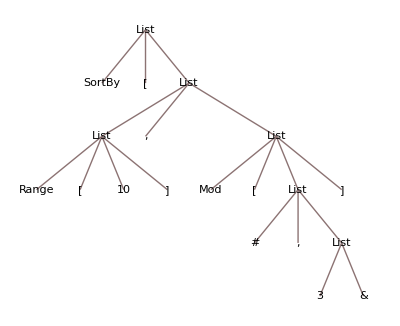

```mathematica
parseInput[mystring]//TreeForm
```

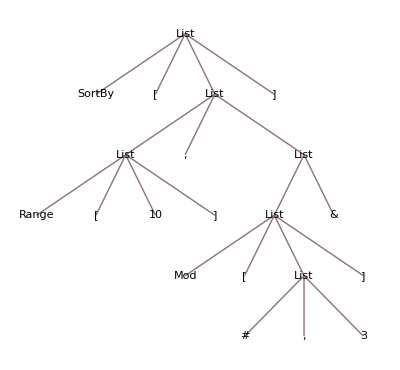

```mathematica
parseInput[mystring]//TreeForm
```

```mathematica
alllevels= getalllevels[mystring];alllevels//Column
```

{SortBy,[,List,]}
{List,,,List}
{Range,[,10,],List,&}
{Mod,[,List,]}
{#,,,3}

```mathematica
listA=Total/@Map[StringCount[#,"["]&,alllevels,{2}]
```

{1,0,1,1,0}

```mathematica
listB=Total/@Map[StringCount[#,"]"]&,alllevels,{2}]
```

{1,0,1,1,0}

```mathematica
Positive[listA-listB]
```

{False,False,False,False,False}

```mathematica
Negative[listA-listB]
```

{False,False,False,False,False}

```mathematica
MapThread[Greater,{listA,listB}]
```

{False,False,False,False,False}

#### Count the # arguments in functions:

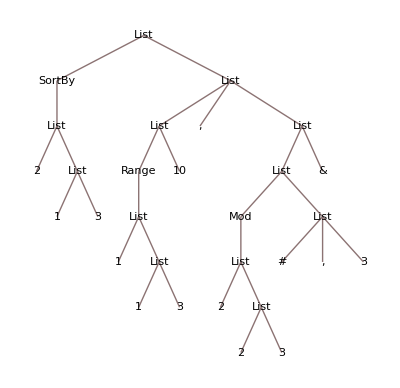

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]"  :> { function[{1+Length@Cases[","]@body,functionargs[function]}], body, lower}//TreeForm
```

#### Other stuff:

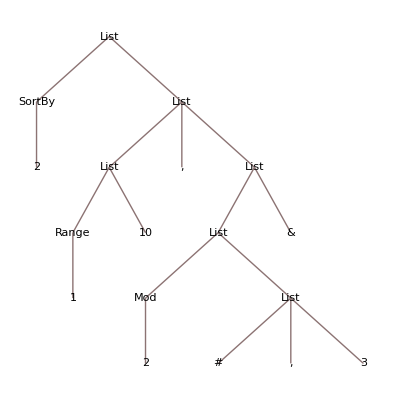

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]"  :> {upper, function[1+Length@Cases[","]@body], body, lower}//TreeForm
```

```mathematica
(*/;Echo[{body,Length[body]},"Body Length"] *)
```

```mathematica
Cases[myexpr,{___,open_,body___,close_,___},Depth[myexpr]]//Column
```

{Range,[,10,]}
{#,,,3}
{Mod,[,{#,,,3},]}
{{Mod,[,{#,,,3},]},&}
{{Range,[,10,]},,,{{Mod,[,{#,,,3},]},&}}

10

## Back to Tim’s Idea:

### (* Convert an expression to a flattened String and try to build the tree correctly *)

#### Initialise:

```mathematica
mystring=makeExpressionString["SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]"]
```

"SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]"

```mathematica
SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]//Hold//TreeForm
```

### Loop Over:

```mathematica
(* Trouble when a functions name is composed out of two other function names: eg IntegerPart -> Integet and Part are also funtions *)
```

```mathematica
(* Take the indexes of the functions that have a head which is a known function and are between brackets. Also they shouldn't include any subfunctions *)
```

```mathematica
(* Not[StringContainsQ[body,"Argument"]]&& *)
```

```mathematica
ranges=StringPosition[mystring,head__~~"["~~body___~~"]"
/; {head}==Names[head]
(*&&StringCases[body,xx__/;Names[xx]=={xx}]=={}*)
(*&& Names[body]== {}*)&&StringCount[body,"["]==StringCount[body,"]"],
Overlaps->All]; ranges//Column
```

{2,41}
{9,40}
{9,25}
{28,40}

### From Giulio:

```mathematica
a[a[a[a[]]]]
```

a[a[a[a[]]]]

```mathematica
str="a[b[], foo[g[Plot[]]]]";
```

```mathematica
level=0;
head=None;
Reap[StringCases[str,{
"[":>Sow[Print["current head is: ", head];level++,"level"],
"]":>Sow[Print["current head is: ", head];level--,"level"],
h:LetterCharacter..:>Sow[head=h,"head"]}
];,_,Rule]
```

current head is: a

current head is: b

current head is: b

current head is: foo

current head is: g

current head is: Plot

current head is: Plot

current head is: Plot

«2 more identical outputs»

{Null,{head→{a,b,foo,g,Plot},level→{0,1,2,1,2,3,4,3,2,1}}}

```mathematica
Join[
Thread[StringPosition[str,"["][[All,1]]->1],
Thread[StringPosition[str,"]"][[All,1]]->-1]
]//KeySort
```

<|2→1,4→1,5→-1,9→1,11→1,13→1,14→-1,15→-1,16→-1,17→-1|>

```mathematica
Accumulate[Values@%]
```

{1,2,1,2,3,4,3,2,1,0}

```mathematica
Plus[Cos[1,2],3]
```

```mathematica
Plus[Cos[1],2,3]
```

```mathematica
Thread[StringPosition[str,"]"][[All,1]]->-1]
```

{5→-1,14→-1,15→-1,16→-1,17→-1}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

SortBy[Range[π argument], Mod[#1, 3 & ]]
Range[π argument], Mod[#1, 3 & ]
Range[π argument]
Mod[#1, 3 & ]

```mathematica
(* Count the arguments each function has *)
```

```mathematica
argnumbers=StringCount[functions,","]+1;argnumbers
```

{1,2}

```mathematica
(* Count the arguments each function should have *)
```

```mathematica
idealargnumbers=functionargs/@Flatten@StringCases[functions,head__ /; {head}==Names[head]:> head]
```

{{1,3},{2,3}}

```mathematica
(* Check if any of the functions has exactly the number of arguments that should be used as input *)
```

```mathematica
exactarguments=Table[{{argnumbers[[i]]}==(Range@@@idealargnumbers)[[i]]},{i,Length[argnumbers]}]//Flatten
```

{False,False}

```mathematica
(* When the arguments are exactly correct, replace with the the string "argument" so it doesn't get picked up again *)
```

```mathematica
(* TO DO: Find the Wolfram whay to do it *)
```

```mathematica
tempstring=mystring;
```

```mathematica
Do[tempstring=StringReplace[tempstring,functions[[ii]]/; exactarguments[[ii]]->"argument"],{ii,Length[argnumbers]}]
```

```mathematica
mystring=tempstring
```

"SortBy[Range[π argument], Mod[#1, 3 & ]]"

### Giulio 3/07

```mathematica
(*
```

```mathematica
level
```

```mathematica
inPartlevel
```

```mathematica
inString
```

```mathematica
inComment
```

```mathematica
{head,argcount,id}
```

```mathematica
j[[
```

```mathematica
[
```

```mathematica
]]
```

```mathematica
,
```

```mathematica
{"w",22->"]"}
```

```mathematica
{"w",-1->"]"}
```

```mathematica
f[[]
```

```mathematica
mystring
```

"SortBy[Range[π Argument], Mod[#1, 3 & ]]"

```mathematica
ranges=StringPosition[mystring,head__~~"["~~body___~~"]"/;Not[StringContainsQ[body,"Argument"]]&& {head}==Names[head]&&StringCases[body,xx__/;Names[xx]=={xx}]=={}&& Names[body]== {}&&StringCount[body,"["]==StringCount[body,"]"],Overlaps->All]; ranges//Column
```

{17,25}
{29,41}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

Cos[10.3]
Mod[#1, 3 & ]

```mathematica
Names["Range[IntegerPart[10.3]], Mod[#1, 3 & ]"]
```

{}

```mathematica
StringCases["Range[IntegerPart[10.3]], Mod[#1, 3 & ]",xx__/; Names[xx]=={xx}]
```

{Range,IntegerPart,Mod}

```mathematica
||Echo[{StringCases[body,xx__/;Names[xx]=={xx}],StringCount[body,"["],StringCount[body,"]"]}]
```

```mathematica
(* Delete the rest *)
```

```mathematica
ranges//Column
```

{17,25}
{29,41}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]
SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]
SortBy[Range[π Cos[10.3]]
SortBy[Range[π Cos[10.3]
Range[π Cos[10.3]], Mod[#1, 3 & ]]
Range[π Cos[10.3]], Mod[#1, 3 & ]
Range[π Cos[10.3]]
Range[π Cos[10.3]
Cos[10.3]], Mod[#1, 3 & ]]
Cos[10.3]], Mod[#1, 3 & ]
Cos[10.3]]
Cos[10.3]
Mod[#1, 3 & ]]
Mod[#1, 3 & ]

```mathematica
StringCases["Range[π Cos[10.3]], Mod[#1, 3 & ]]","["~~"]"]
```

{}

```mathematica
<|2->{2,3},1->{ 3,4}|>
```

<|2→{2,3},1→{3,4}|>

```mathematica
%35[2]
```

{2,3}

## Function pattern matching from Tim

```mathematica
SyntaxInformation[AASTriangle]
```

```mathematica
{"ArgumentsPattern"->{_,_,_}}
```

```mathematica
symbolsWithInfo = GroupBy[Names["System`*"][[117;;]], Lookup[Association[SyntaxInformation[Symbol[#]]],"ArgumentsPattern"]=!={___}&]
```

```mathematica
Length@Names["System`*"][[117;;]]
```

6490

```mathematica
Length@symbolsWithInfo
```

6350

```mathematica
f[g[h[a,b,c],t]
```

```mathematica
symbolsSignatures = GroupBy[Names["System`*"][[117;;]], Lookup[Association[SyntaxInformation[Symbol[#]]],"ArgumentsPattern"]&];
```

```mathematica
{_,_.,_.,_.,_.}->{"CMYKColor","StableDistribution"}
```

```mathematica
?CMYKColor
```

```mathematica
{_,{__},OptionsPattern[]}
```

```mathematica
"BooleanRegion"
```

```mathematica
BooleanRegion[Xor,{Disk[{-1/3,0},1],Disk[{1/3,0},1]}]
```

```mathematica
...Multicolumn[Table[BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7]],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}],2]
```

```mathematica
...BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}...
```

```mathematica
MatchQ[{op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}
},{_,{__},OptionsPattern[]}]
```

False

```mathematica
BooleanRegion[op,{a,b}],PlotLabel-> …
```

```mathematica
BooleanRegion[op,{a,b},PlotLabel-> op],BaseStyle->…
```

```mathematica
BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7]],{op, …
```

```mathematica
ToString[f["the string"],InputForm]
```

```mathematica
{"f","[","\"the string\"","]"}
```

```mathematica
{exp1,Nothing,exp13, exp2, Nothing}
```

{exp1,exp13,exp2}

```mathematica
data = {<|"a"-><|"a"->"a1"|>,"b"-><|"b"->"b1"|>|>, <|"a"-><|"a"->"a2"|>,"b"-><|"b"->"b2"|>|>};
```

```mathematica
data[[All, All, "a"]]
```

{<|a→a1,b→Missing[KeyAbsent,a]|>,<|a→a2,b→Missing[KeyAbsent,a]|>}

## Look at this:

```mathematica
str="a[b[],foo[g[Plot[]]]]";
```

```mathematica
str="a[b[cc[d[e[foo[t, h[x]]]]]]]";
```

```mathematica
TreeForm@Hold@SortBy[Range[Cos[x],Cos[x]+4, Mod[#1, 3 & ]]
```

#### I create this array:

```mathematica
treestructure=.
```

```mathematica
treestructure//SortBy[#[[1]]&]//Reverse//Dataset
```

Dataset[<>]

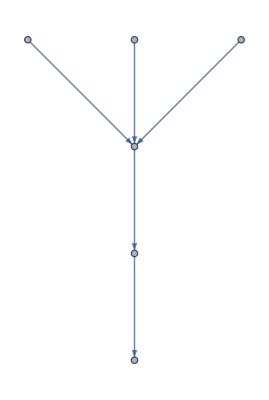

```mathematica
Lookup["parent"]/@treestructure//Normal//Graph
```

### To do: How to match the pattern?

```mathematica
MatchQ[ToExpression["List[a,b,c]"],{_,_.,_.}]
```

True

```mathematica
SortBy
```

```mathematica
MatchQ[ToExpression["List[a,b]"],Replace[{_,_.,_.},Verbatim[Optional][x_]:>Repeated[x,{0,1}],1]]
```

True

```mathematica
Replace[{_,_.,_.},Verbatim[Optional][x_]:>Repeated[x,{0,1}],1]
```

{_,Repeated[_,{0,1}],Repeated[_,{0,1}]}

```mathematica
MatchQ[ToExpression["List[a,b]"],{_,___}]
```

True

### Implementation

```mathematica
gghd
```

gghd

```mathematica
str="SortBy[Range[Cos[x],Cos[x]+1, Mod[#1, 3 & ]]"
```

SortBy[Range[Cos[x],Cos[x]+1, Mod[#1, 3 & ]]

```mathematica
StringTake[str,;;20]
```

SortBy[Range[Cos[x],

```mathematica
{"SortBy[Range[Cos[x]],Cos[x]+1, Mod[#1, 3 & ]]]",
"SortBy[Range[Cos[x],Cos[x]+1], Mod[#1, 3 & ]]"
}
```

Idea: The id should contain the current level + a unique id
previous head should be: Function Head: {level, unique id} ->  head, Current Number of Arguments, Key of parent Function

#### Two options: fork, or generate a list of possible changes. Maybe try both

#### Check for

```mathematica
level=0;head=None;treestructure=Association[<| |>];id=1;commasfound=0;suggestions={};
Reap[StringCases[str,{
"[":>
Sow[Print["Going Down",treestructure],
level++;
id=whatismyid[level];
treestructure=Append[
treestructure,{level,id+1}-> Association@@
{"head"-> head,
"argnumber"-> 1,
If[level>1,
"parent"-> (Keys@KeySelect[treestructure,#[[1]]==(level-1)&])[[-1]],
"parent"->{0,0}
],
"pattern"-> "_"
}
];
Print["current level, id, head is: ",level," ",id, " ", head];],
"]":>Sow[Print["Going Up",treestructure],
level--;
id=whatismyid[level];
Print["current level, id, head is: ",level," ",id, " ", head];
If[level>0,
head=treestructure[{level,id}][[1]],head=" "];
Print["current level, id, head is: ",level," ",id, " ", head];],
h:LetterCharacter..:>Sow[head=h,"head"],
",":> Sow[Print["A comma was found at position ", commapositions[[commasfound+1]]];
id=whatismyid[level];
matches= MatchQ[ ToExpression[ StringJoin[ "{",treestructure[{2,1},"pattern"],"}" ] ], Replace[Lookup[SyntaxInformation[Symbol@treestructure[{2,1},"head"]], "ArgumentsPattern"],Verbatim[Optional][x_]:>Repeated[x,{0,1}],1]];
Print["Current function pattern matches correct function",matches];
If[matches,
newexpr=StringJoin[StringTake[str,;;commapositions[[commasfound+1]]-1],"]",StringTake[str,commapositions[[commasfound+1]];;]];If[Length@StringCases[newexpr,"["]==Length@StringCases[newexpr,"]"],suggestions=Append[suggestions,newexpr]];];
commasfound++;
treestructure=Append[treestructure,{level,id}->Association@@
{"head"-> treestructure[{level,id},"head"],
"argnumber"-> treestructure[{level,id},"argnumber"]+1,
"parent"-> treestructure[{level,id},"parent"],
"pattern"-> StringJoin[treestructure[{level,id},"pattern"],", _"]
}
]
]}
];,_,Rule];
```

Going Down<||>

current level, id, head is: 1 0 SortBy

Going Down<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>|>

current level, id, head is: 2 0 Range

Going Down<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>,{2,1}→<|head→Range,argnumber→1,parent→{1,1},pattern→_|>|>

current level, id, head is: 3 0 Cos

Going Up<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>,{2,1}→<|head→Range,argnumber→1,parent→{1,1},pattern→_|>,{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>|>

current level, id, head is: 2 1 x

current level, id, head is: 2 1 Range

A comma was found at position 20

Current function pattern matches correct functionTrue

Going Down<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>,{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{2,1}→<|head→Range,argnumber→2,parent→{1,1},pattern→_, _|>|>

current level, id, head is: 3 1 Cos

Going Up<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>,{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{2,1}→<|head→Range,argnumber→2,parent→{1,1},pattern→_, _|>,{3,2}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>|>

current level, id, head is: 2 1 x

current level, id, head is: 2 1 Range

A comma was found at position 29

Current function pattern matches correct functionTrue

Going Down<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>,{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{3,2}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{2,1}→<|head→Range,argnumber→3,parent→{1,1},pattern→_, _, _|>|>

current level, id, head is: 3 2 Mod

A comma was found at position 37

Current function pattern matches correct functionTrue

Going Up<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>,{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{3,2}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{2,1}→<|head→Range,argnumber→3,parent→{1,1},pattern→_, _, _|>,{3,3}→<|head→Mod,argnumber→2,parent→{2,1},pattern→_, _|>|>

current level, id, head is: 2 1 Mod

current level, id, head is: 2 1 Range

Going Up<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>,{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{3,2}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{2,1}→<|head→Range,argnumber→3,parent→{1,1},pattern→_, _, _|>,{3,3}→<|head→Mod,argnumber→2,parent→{2,1},pattern→_, _|>|>

current level, id, head is: 1 1 Range

current level, id, head is: 1 1 SortBy

```mathematica
suggestions//Column
```

SortBy[Range[Cos[x]],Cos[x]+1, Mod[#1, 3 & ]]
SortBy[Range[Cos[x],Cos[x]+1], Mod[#1, 3 & ]]
SortBy[Range[Cos[x],Cos[x]+1, Mod[#1], 3 & ]]

```mathematica
ToExpression[suggestions[[2]]]
```

{Cos[x],1+Cos[x]}

```mathematica
Length@StringCases[suggestions[[1]],"["]==Length@StringCases[suggestions[[1]],"]"]
```

True

#### From Discussion with Tim: better to actually built the tree along the way, match and fork (recursive function?) when needed. Also, match

```mathematica
Lookup[SyntaxInformation[Plot], "ArgumentsPattern"]
```

{_,_,OptionsPattern[]}

```mathematica
Print["Current function pattern matches:",MatchQ[ToExpression[StringJoin["{",treestructure[{2,1},"pattern"],"}"]],Replace[Lookup[SyntaxInformation[Symbol@treestructure[{2,1},"head"]], "ArgumentsPattern"],Verbatim[Optional][x_]:>Repeated[x,{0,1}],1]]];
```

Current function pattern matches:True

## Actual Work:

## Build the function:

### complementary functions:

```mathematica
FindCommaPositions[thisString_?StringQ]:=StringPosition[thisString,","][[All,1]];
```

```mathematica
whatismyid[currentlevel_,thistreeStructure_]:=Length@KeySelect[thistreeStructure,#[[1]]==currentlevel&];
```

```mathematica
newTreeEntry[level_,id_,head_,treeStructure_]:=
	{level,id+1}-> 
		Association@@
		{
			"head"-> head,
			"argnumber"-> 1,
			If[level>1,
				"parent"-> (Keys@KeySelect[treeStructure,#[[1]]==(level-1)&])[[-1]],
				"parent"->{0,0}
			],
			"pattern"-> "_"
		}
```

```mathematica
testPatternMatch[treeStructure_,level_,id_]:=
	MatchQ[ 
		ToExpression[ 
			StringJoin[ 
				"{",
				treeStructure[{level,id},"pattern"],
				"}" 
			] 
		], 
	Replace[
		Lookup[
			SyntaxInformation[
				Symbol@
					treeStructure[{level,id},"head"]], 
			"ArgumentsPattern"
		],
		Verbatim[Optional][x_]:>Repeated[x,{0,1}],1
	 ]
]
```

```mathematica
createAlternativeExpr[str_?StringQ..,commaPositions_,commasFound_]:=
"]"<>StringTake[str,commaPositions[[commasFound+1]]+1;;]
(*	StringJoin[
		StringTake[str,;;commaPositions[[commasFound+1]]-1],
		"]",
		StringTake[str,commaPositions[[commasFound+1]];;]
	]*)
```

```mathematica
(* THIS IS ALWAYS TRUE FOR NOW BEFORE EACH RECURSIVE FUNCTION TAKES A SHORTER AND SHORTER STRING *)
(*CheckSyntax[newExpr_]:= 1 == 1
Length@
	StringCases[newExpr,"["]==
Length@
StringCases[newExpr,"]"]*)
```

```mathematica
updateTreeEntry[level_,id_,treeStructure_]:=
	{level,id}->
		Association@@
		{
			"head"-> treeStructure[{level,id},"head"],
			"argnumber"-> treeStructure[{level,id},"argnumber"]+1,
			"parent"-> treeStructure[{level,id},"parent"],
			"pattern"-> StringJoin[treeStructure[{level,id},"pattern"],", _"]
		}
```

### treeBuilder function:

```mathematica
treeBuilder[str_?StringQ,thistreeStructure_,thislevel_?IntegerQ,thisid_?IntegerQ,thishead_?StringQ]:=
	Module[
		{suggestions={},
		level=thislevel,
		treeStructure=thistreeStructure,
		head=thishead,
		commasFound=0,
		(*commasFound=thisCommasFound,*)
		id = thisid,
		commaPositions=FindCommaPositions[str]
		},
Reap[
	StringCases[
		str,
		{
		"[":>
			Sow[If[level > 0 || treeStructure == Association[<| |>], Print["Going Down"(*,treeStructure*)];
			level=level+1;
			id = whatismyid[level,treeStructure];
			treeStructure=
				Append[
				treeStructure,newTreeEntry[level,id,head,treeStructure]
				];
			Print["current level, id, head is: ",level," ",id, " ", head]]],
		"]":>If[level > 0,Sow[Print["Going Up"(*,treeStructure*)],
			level--;
			id = whatismyid[level,treeStructure];
			If[level>0,
				head=treeStructure[{level,id}][[1]],head=" "];
				Print["current level, id, head is: ",level," ",id, " ", head];],level--],
		h:LetterCharacter..:>Sow[head=h,"head"],
		",":> If[level > 0, Sow[Print["A comma was found at position ", commaPositions[[commasFound+1]]];
		id = whatismyid[level,treeStructure];
		matches= testPatternMatch[treeStructure,level,id];
		(*Print["Current function pattern matches correct function: ",matches];*)
		(*newExpr = createAlternativeExpr[str,commaPositions,commasFound];*)
		(*passedChecks=CheckSyntax[newExpr];*)
		If[matches,
			Print["Branching for: ", "]"<>StringTake[str,commaPositions[[commasFound+1]]+1;;]]; 
			suggestions = Flatten @ Append[suggestions,treeBuilder[createAlternativeExpr[str,commaPositions,commasFound],treeStructure,level,id,head]]
			];
		commasFound++;
		treeStructure=
			Append[
				treeStructure,
				updateTreeEntry[level,id,treeStructure]
				  ]
				]]
		}
	];,_,Rule];
	Which[
		level < 0,
			Print["We do not like that one"],
		level == 0,
			suggestions = Append[suggestions,treeStructure],
		level>0, suggestions = Flatten @ Append[suggestions,treeBuilder["]",treeStructure,level,id,head]];
			];
	(*If[level==0,
		,
		];*)
	Print["LEVEL: ",level];
	Print["SUGGESTIONS: ",str,suggestions];
	Print["End of Branching   "];
	suggestions
]
```

### main function:

```mathematica
errorExplorer[str_?StringQ]:=
	Module[
	{
		level = 0,
		head = "None",
		treeStructure = Association[<| |>],
		id=1,
		commasFound = 0,
		(*suggestions={},*)
		commaPositions = FindCommaPositions[str]
	},
	treeBuilder[str,treeStructure,level,id,head]
]
```

## Test the function:

```mathematica
str="SortBy[Range[Cos[x],Cos[x]+1], Mod[#1, 3 & ]]"
```

SortBy[Range[Cos[x],Cos[x]+1], Mod[#1, 3 & ]]

```mathematica
suggestions=errorExplorer[str];
```

Going Down

current level, id, head is: 1 0 SortBy

Going Down

current level, id, head is: 2 0 Range

Going Down

current level, id, head is: 3 0 Cos

Going Up

current level, id, head is: 2 1 Range

A comma was found at position 20

Branching for: ]Cos[x]+1], Mod[#1, 3 & ]]

Going Up

current level, id, head is: 1 1 SortBy

Going Down

current level, id, head is: 2 1 Cos

Going Up

current level, id, head is: 1 1 SortBy

Going Up

current level, id, head is: 0 0

We do not like that one

LEVEL: -2

SUGGESTIONS: ]Cos[x]+1], Mod[#1, 3 & ]]{}

End of Branching

Going Down

current level, id, head is: 3 1 Cos

Going Up

current level, id, head is: 2 1 Range

Going Up

current level, id, head is: 1 1 SortBy

A comma was found at position 30

Branching for: ] Mod[#1, 3 & ]]

Going Up

current level, id, head is: 0 0

We do not like that one

LEVEL: -2

SUGGESTIONS: ] Mod[#1, 3 & ]]{}

End of Branching

Going Down

current level, id, head is: 2 1 Mod

A comma was found at position 38

Going Up

current level, id, head is: 1 1 SortBy

Going Up

current level, id, head is: 0 0

LEVEL: 0

SUGGESTIONS: SortBy[Range[Cos[x],Cos[x]+1], Mod[#1, 3 & ]]{<|{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{2,1}→<|head→Range,argnumber→2,parent→{1,1},pattern→_, _|>,{3,2}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{1,1}→<|head→SortBy,argnumber→2,parent→{0,0},pattern→_, _|>,{2,2}→<|head→Mod,argnumber→2,parent→{1,1},pattern→_, _|>|>}

End of Branching

```mathematica
suggestions//Length
```

1

```mathematica
suggestions[[1]]//SortBy[#[[1]]&]//Reverse//Dataset
```

Dataset[<>]

## Visualise the tree:

```mathematica
Manipulate[keys=Keys[suggestions[[ii]]];names=(suggestions[[ii]]//Values)[[All,"head"]];forgraph=AssociationThread[keys->names]//Normal;Graph[Lookup["parent"]/@suggestions[[ii]]//Normal,VertexLabels->forgraph,VertexSize->Large],{{ii,1,"Suggestion"},1,Length@suggestions,1}]
```

## To do:

### Find a better way to visualise differences - currently returning the whole tree Make the Search recursive - Fork (Kind of did that) Then implement: Two missing brackets (any number of missing closing brackets implemented) or one/two extra brackets Then implement: inPartlevel, inString, inComment Also, implement branching for closing brackets